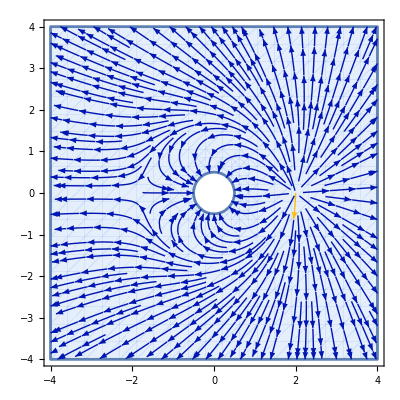

```mathematica
(*Define parameters*)R=0.5;
s=2; (*Set a value for s,if unspecified*)

(*Define the vector field components in polar coordinates*)
vr[r_,theta_]:=(2 r-2 s Cos[theta])/(2 (r^2+s^2-2 r s Cos[theta])^(3/2))-((2 r s^2)/R^2-2 s Cos[theta])/(2 (R^2+(r^2 s^2)/R^2-2 r s Cos[theta])^(3/2));
vtheta[r_,theta_]:=-((-((r s Sin[theta])/(r^2+s^2-2 r s Cos[theta])^(3/2))+(r s Sin[theta])/(R^2+(r^2 s^2)/R^2-2 r s Cos[theta])^(3/2))/r);

(*Convert polar to Cartesian components*)
vx[x_,y_]:=Module[{r=Sqrt[x^2+y^2],theta=ArcTan[x,y]},vr[r,theta] Cos[theta]-vtheta[r,theta] Sin[theta]];
vy[x_,y_]:=Module[{r=Sqrt[x^2+y^2],theta=ArcTan[x,y]},vr[r,theta] Sin[theta]+vtheta[r,theta] Cos[theta]];

(*Plot the vector field in Cartesian coordinates for r>R*)
StreamPlot[{vx[x,y],vy[x,y]},{x,-4,4},{y,-4,4},RegionFunction->Function[{x,y,u,v},Sqrt[x^2+y^2]>R],StreamPoints->Fine,PlotRange->All]
```

```mathematica
((((((((((((((((((((((((((((((((((((((((((((((((((((((((((((((((((((((((((((((((((((□^□)^□)^□)^□)^□)^□)^□)^□)^□)^□)^□)^□)^□)^□)^□)^□)^□)^□)^□)^□)^□)^□)^□)^□)^□)^□)^□)^□)^□)^□)^□)^□)^□)^□)^□)^□)^□)^□)^□)^□)^□)^□)^□)^□)^□)^□)^□)^□)^□)^□)^□)^□)^□)^□)^□)^□)^□)^□)^□)^□)^□)^□)^□)^□)^□)^□)^□)^□)^□)^□)^□)^□)^□)^□)^□)^□)^□)^□)^□)^□)^□)^□)^□)^□)^□
```

```mathematica
((((((((((((((□^□)^□)^□)^□)^□)^□)^□)^□)^□)^□)^□)^□)^□)^□)^□
```